# Лабораторная работа 3. Уравнения колебаний

## 3.1. Задача о граничных условиях на пружинный осциллятор.

### Собственная длина пружины 0.2м, длина сжатой полностью пружины 0.1м. Жесткость 250Н/м. Масса маятника 0.1кг. В этой задаче мы интересуемся применимостью модели. Задачи:

### a. Найти область в фазовом пространстве, при выборе значений из которой будут происходить колебания без удара о стенку.

```mathematica
l=0.2;
l1=0.1;
k=250;
m=0.1;
```

```mathematica
w=Sqrt[k/m]
```

50.

m a =F
m (d^2 x)/dt^2=-kx
Линейное дифференциальное уравнение второго порядка, однородное, с постоянными коэффициентами.
m (d^2 x)/dt^2+kx=0
Общее решение:
x(t)=C_1 e^(t_1 t)+C_2 e^(t_2 t)=C_1 sin √(k/m) t + C_2 cos √(k/m)t
x(t)=C_1 sin wt + C_2 cos wt, где w = √(k/m)
x(t)=A sin (wt+δ), где A=C_1^2+C_2^2, w = √(k/m)
Имеем задачу Коши:
x(t)=C_1 sin wt + C_2 cos wt,
       x(0)=x_0
       x'(0)=v_0

```mathematica
x[t_]:=A Sin[w t+δ]
```

Скорость как производная по времени

```mathematica
v[t_]:=D[x[t],t]
```

Энергия постоянная, поэтому:
E(t)=E_k+E_п=(m(x'(t))^2)/2+k/2(x(t))^2=1/2(k x_0^2+m v_0^2)≤E_max, где E_max - потенциальная энергия полностью сжатой пружины.

```mathematica
Emax =(k*(0.1)^2)/2
```

1.25

Имеем уравнение
k x_0^2+m v_0^2≤k x1^2
x_0^2/x_0^2+v_0^2/((k x_0^2)/m)≤1

```mathematica
area[v0_,x0_]:=k*x0^2+m*v0^2-k*l1^2≤0
```

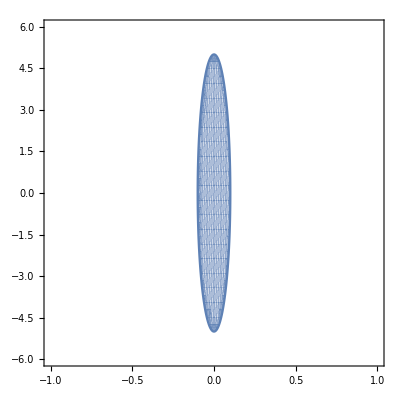

```mathematica
RegionPlot[area[v,x],{x,-.1,.1},{v,-5,5},PlotRange->{{-1,1},{-6,6}}]
```

То есть если точка расположена внутри эллипса, то ударов о стенку нет.
Если же вне эллипса, то есть.

### b. Описать поведение маятника в регулярном случае анимированными графиками координаты от времени и фазового пространства.

Имеем уравнение
x_0^2/x_0^2+v_0^2/((k x_0^2)/m)≤1

Найдем значение амплитуды для равенства

```mathematica
x0=0.05;
v0=2;
```

```mathematica
δ=0;
```

```mathematica
Solve[{(x0/A)^2+(v0/(w*A))^2==1,A>0},A]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{A→0.0640312}}

```mathematica
A=0.0640;
```

```mathematica
x[t_]:=A Sin[w t]
```

```mathematica
Manipulate[Show[{Plot[A Sin[w t],{t,0,2π}],Graphics[{PointSize[Large],Point[{t,A Sin[w t]}]}]}],{t,0,2π}]
```

### c. Описать поведение маятника в не регулярном случае анимированными графиками координаты от времени и фазового пространства. В предположении потери 10% энергии при каждом ударе.

## 3.2. Задача о ущербности линейной аппроксимации

Сравнить поведение линейного и синусоидального осциллятора типа маятник. Найти момент времени, в который эти осцилляторы удалятся друг от друга на величину амплитуды колебаний. Длина нити 1м. Начальное отклонение 0.2рад.

## 3.3. Пружинный маятник на наклонной поверхности. Принцип Гамильтона.

Построить математическую модель движения пружинного осциллятора на НАКЛОННОЙ поверхности с помощью принципа Гамильтона (см. пример в Самарском). Как учесть в такой модели силу трения о поверхность?